# RandomMixedGraph

RandomMixedGraph[{vertices,edges},threshhold] 
creates a random mixed graph with vertices vertices and edges edges composed up of threshhold directed edges

## Tech NotesTechNotesInsert links to related tech notes.

## Related LinksRelatedLinksInsert links to any related page, including web pages.

## See AlsoSeeAlsoInsert links to any related reference (function) pages. Type a space, a period and then another space between function names. Then click the palette's Inline Listing Toggle button.

## Related Guides

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

## Basic Examples | More Examples ⊳

Make a random mixed graph with 20 nodes and 48 edges with 77% of the edges directed:

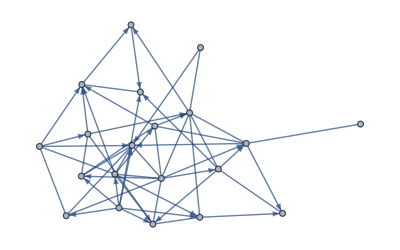

```mathematica
RandomMixedGraph[{20,54},0.77]
```

Construct a graph with 30% directed edges:

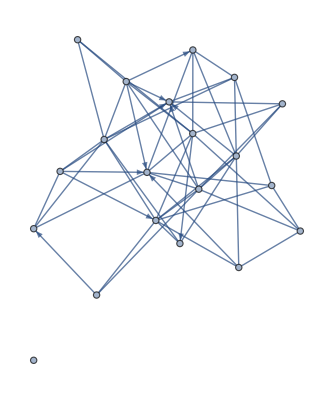

```mathematica
RandomMixedGraph[{20,54},0.30]
```

Make a list of random mixed graphs:

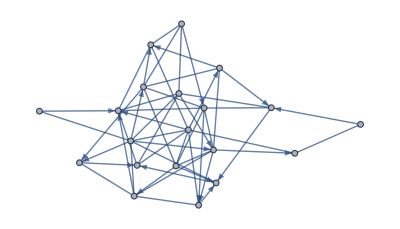
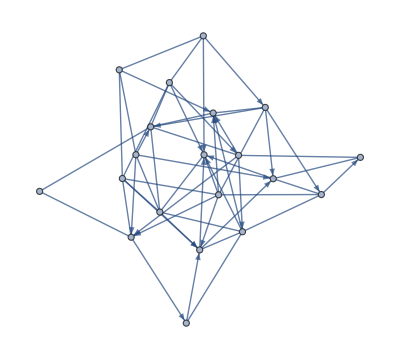
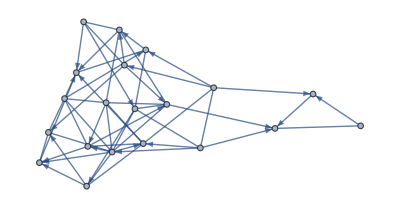
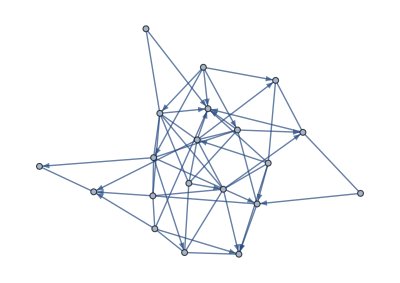
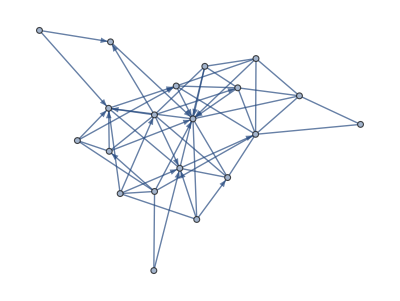
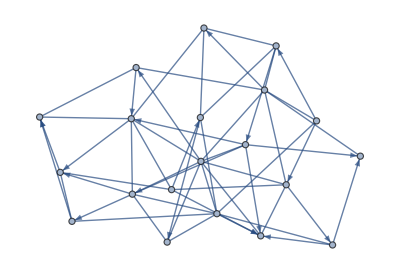
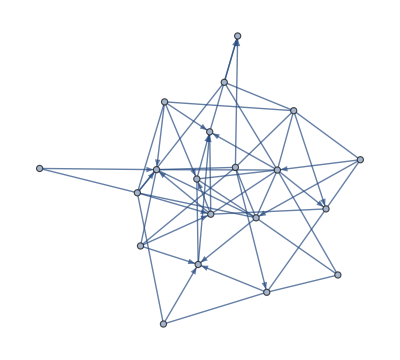

```mathematica
RandomMixedGraph[{20,54},0.7,7]
```

Make an array of mixed graphs:

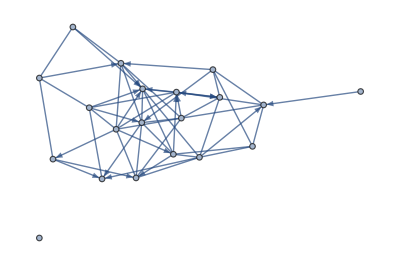
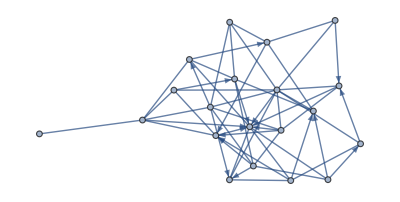
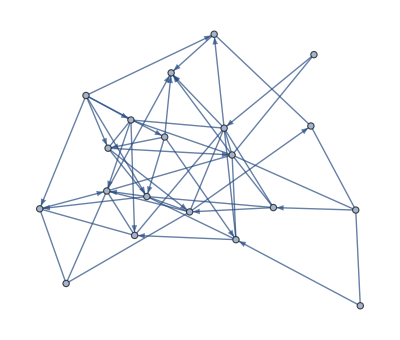
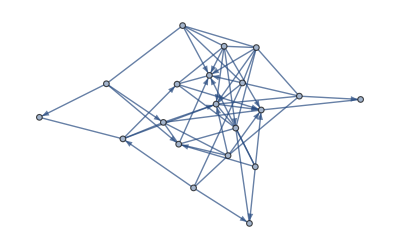
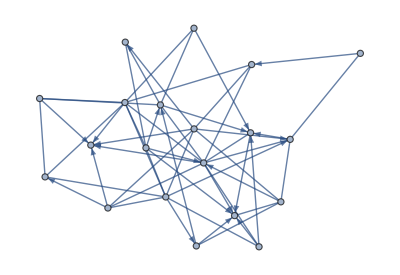
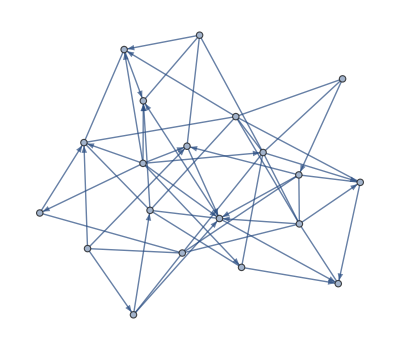
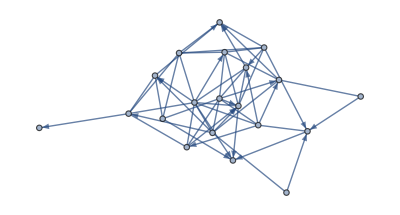
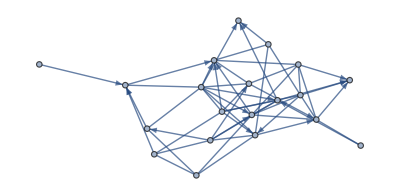

```mathematica
RandomMixedGraph[{20,54},0.7,{3,7}]
```

Create a mixed graph from a graph distribution.

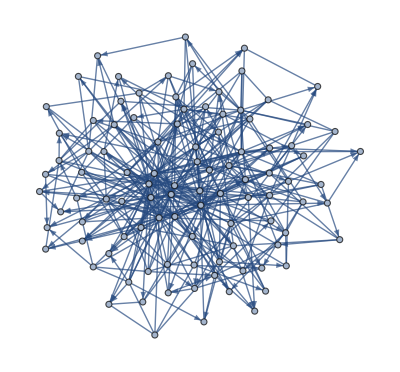

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[100,4],0.68]
```

Create a list of random mixed graphs with a graph distribution:

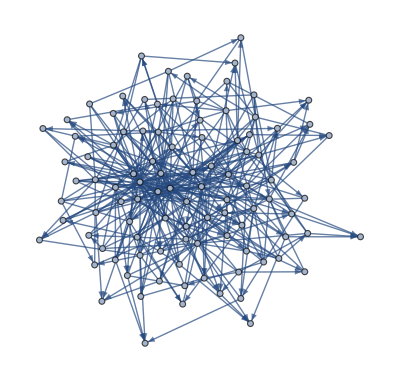
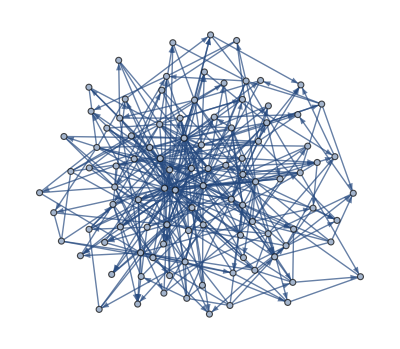
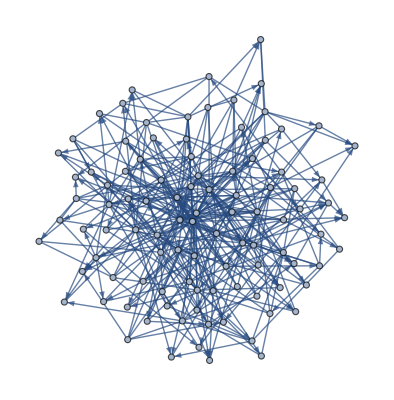
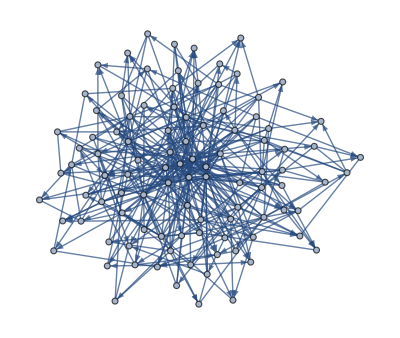
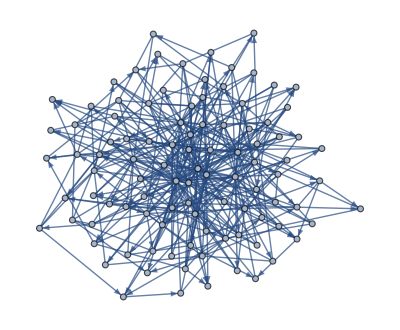
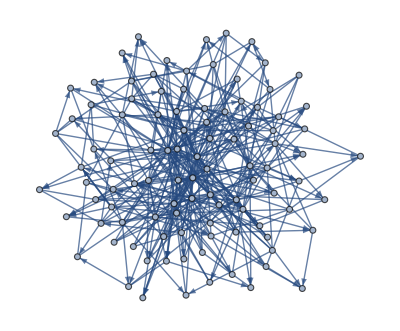
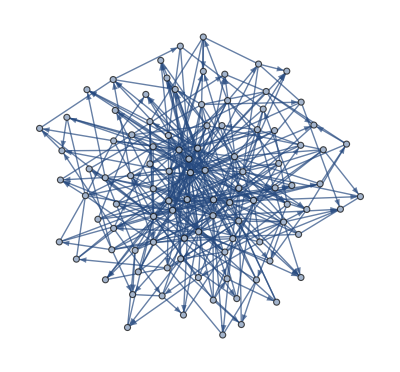

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[100,4],0.68,7]
```

Create an array of mixed graphs from a graph distribution:

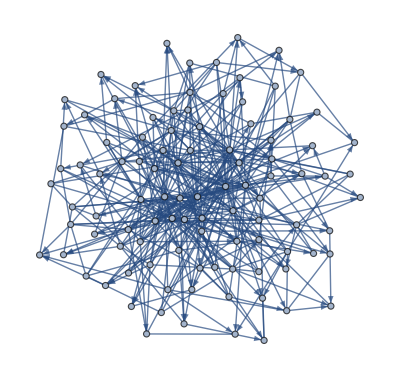
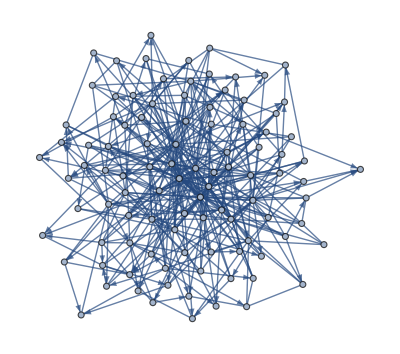
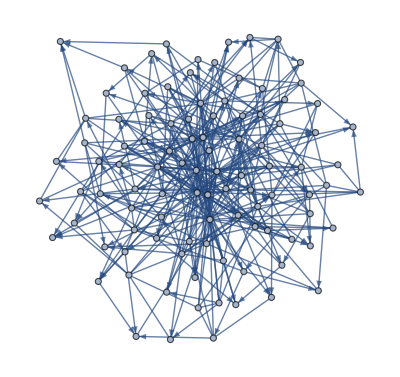
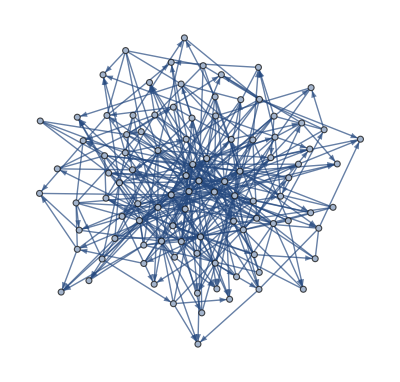
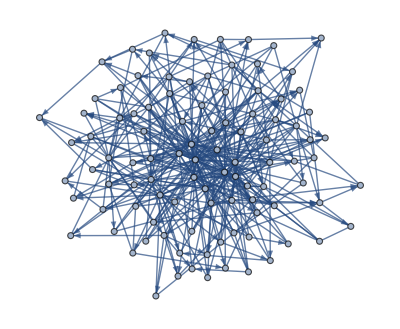
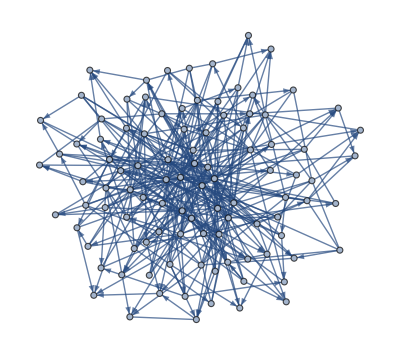
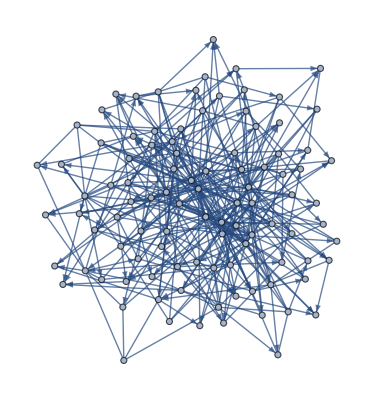
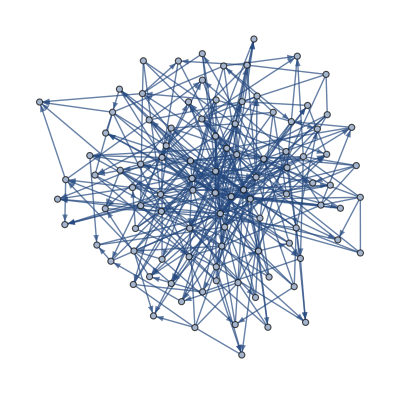

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[100,4],0.68,{7,3}]
```

Create an array of random mixed graphs with a graph distribution:

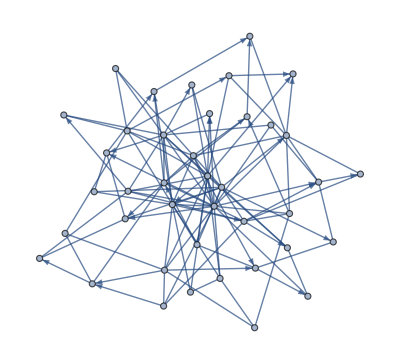
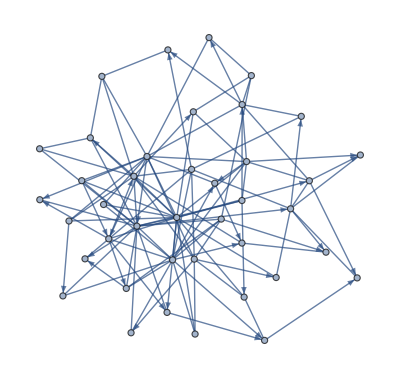
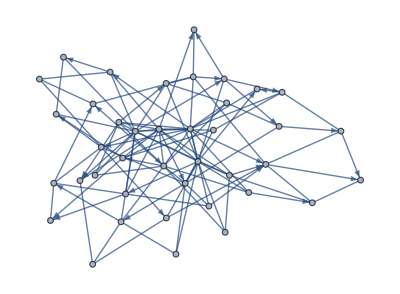
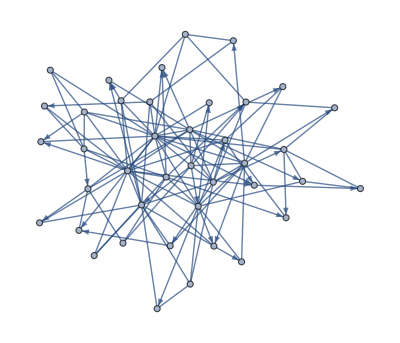
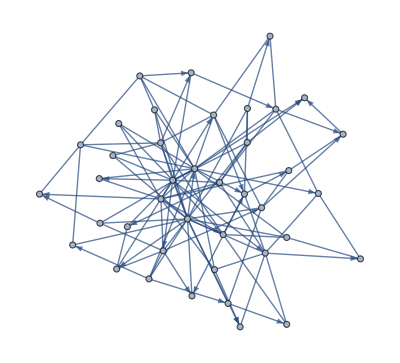
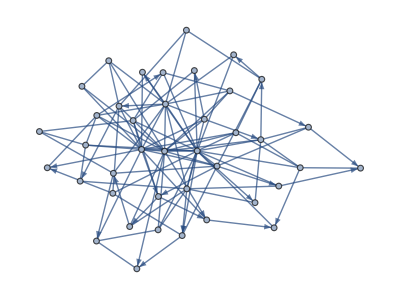
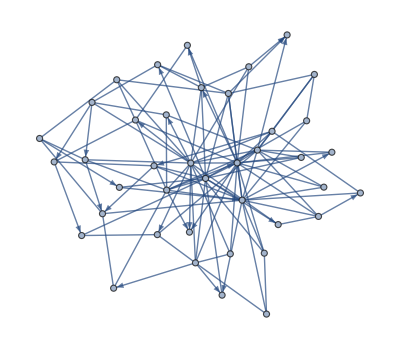
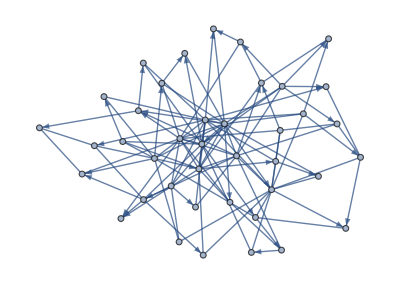

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[30,2],.5,{3,4}]
```

Create an array of random mixed graphs:

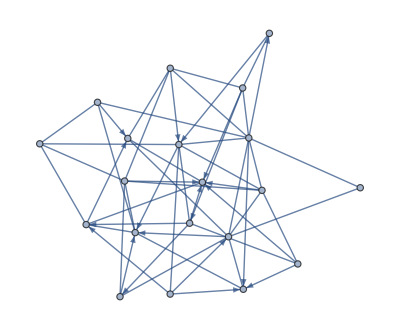
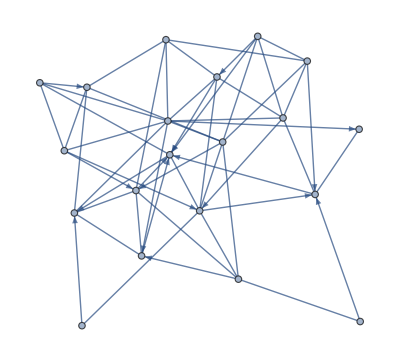
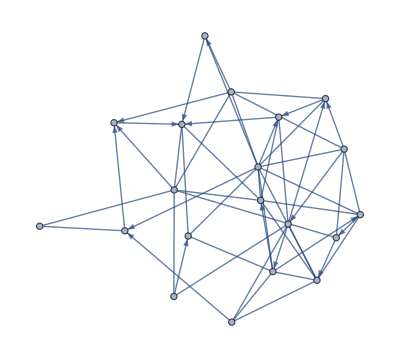
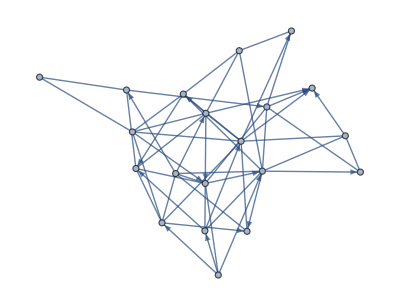
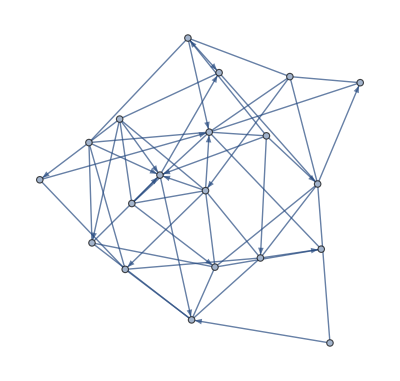
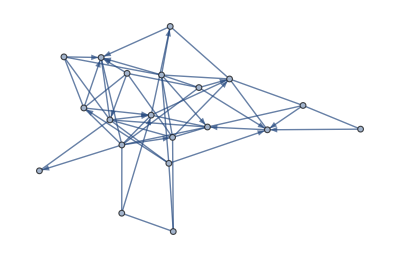

```mathematica
RandomMixedGraph[{20,54},.5,{2,3}]
```

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

### Generalizations & Extensions

### Options

### Applications

Create a random spatial graphs

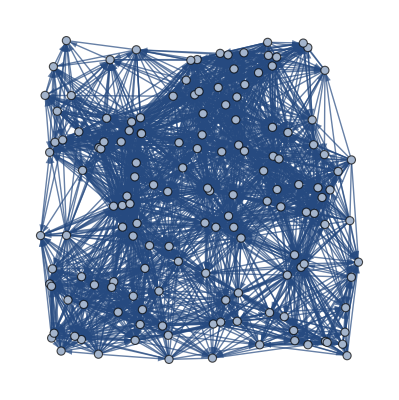

```mathematica
RandomMixedGraph[SpatialGraphDistribution[148,1-0.68],0.68]
```

There is a snowball fight with 144 people. The probability of being hit is 0.14. Make a graph of the interaction

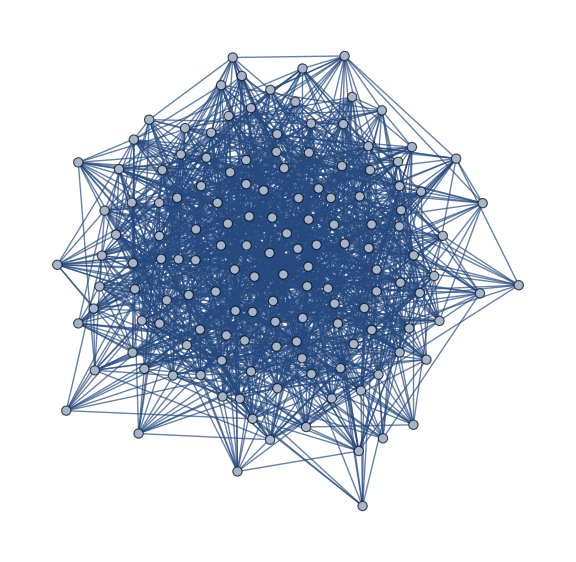

```mathematica
Graph[RandomMixedGraph[BernoulliGraphDistribution[144,0.14],0],ImageSize->Large]
```

### Applications

Make a big mixed graph:

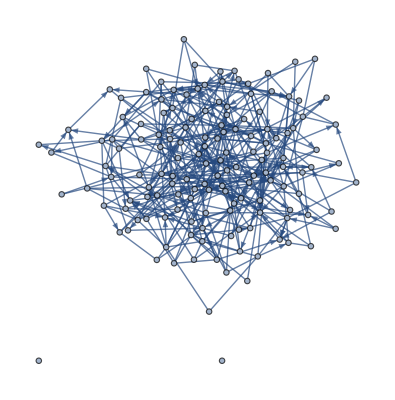

```mathematica
RandomMixedGraph[{148,403},0.68]
```

Create a really big mixed graph:

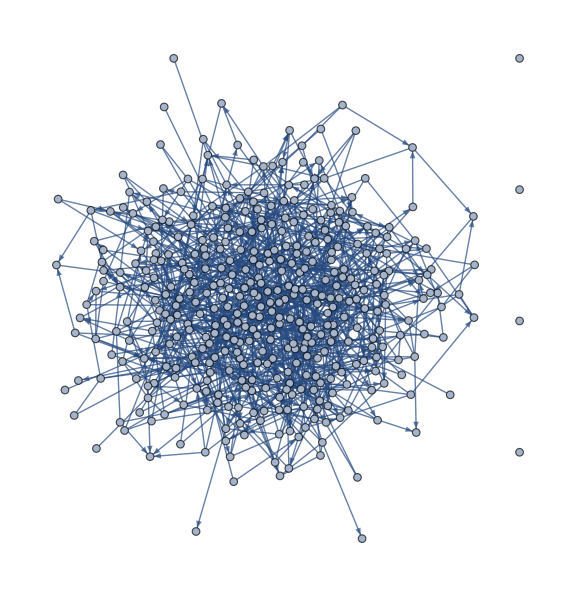

```mathematica
Graph[RandomMixedGraph[{403,1096},0.68],ImageSize->Large]
```

Verify the output of the function produces a mixed graph:

```mathematica
MixedGraphQ[RandomMixedGraph[{148,403},.75]]
```

True

Evaluate if a mixed graph has a Hamiltonian cycle:

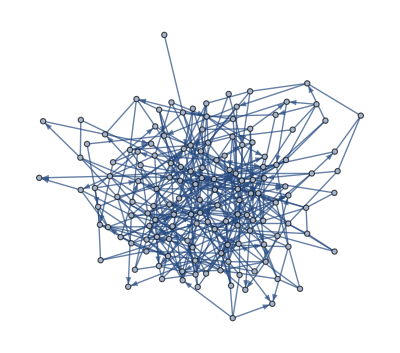

```mathematica
𝒢=RandomMixedGraph[{148,403},ⅇ^-1]
```

```mathematica
HamiltonianGraphQ[𝒢]
```

False

Find the graph union of two mixed graphs:

```mathematica
GraphUnion@@Table[RandomMixedGraph[{20,54},.75],3]
```

-Graphics-

Make an indexed mixed graph:

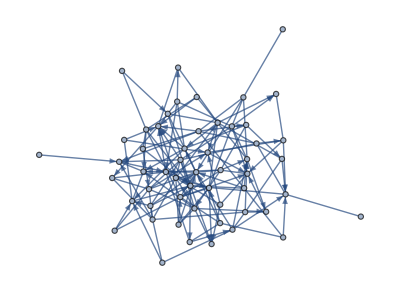

```mathematica
IndexGraph[RandomMixedGraph[{54,148},.75]]
```

Reverse a mixed graph's directed edges:

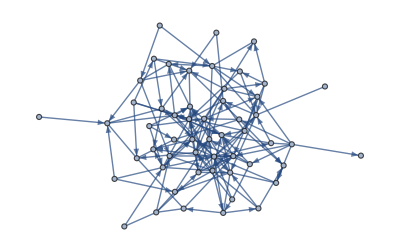

```mathematica
ReverseGraph[RandomMixedGraph[{54,148},.7]]
```

Apply binary graph operations to two small mixed graphs:

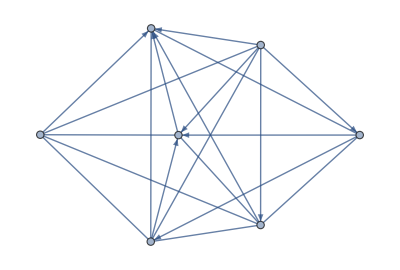

```mathematica
𝒢=RandomMixedGraph[{7,20},.77]
```

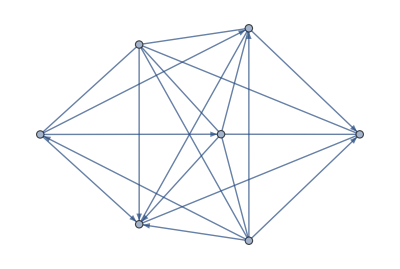

```mathematica
ℋ=RandomMixedGraph[{7,20},.77]
```

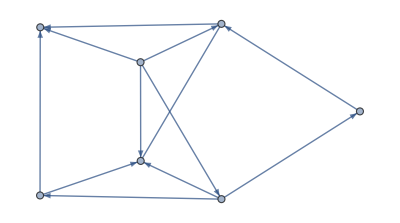
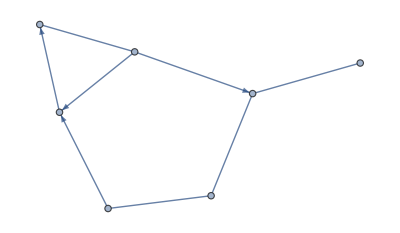
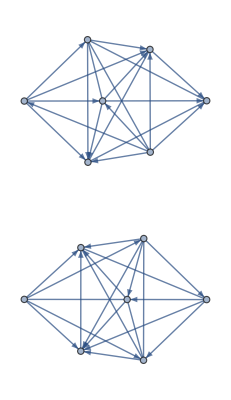
<|(BooleanGraph[Xor,##1]&)→-Graphics-,(BooleanGraph[Nand,##1]&)→-Graphics-,GraphIntersection→-Graphics-,GraphUnion→-Graphics-,GraphDifference→-Graphics-,GraphDisjointUnion→-Graphics-,GraphProduct→-Graphics-,GraphJoin→-Graphics-,GraphSum→-Graphics-|>

```mathematica
AssociationMap[(graphOperation↦graphOperation[𝒢,ℋ]),{BooleanGraph[Xor,##]&,BooleanGraph[Nand,##]&,GraphIntersection,GraphUnion,GraphDifference,GraphDisjointUnion,GraphProduct,GraphJoin,GraphSum}]
```

Evaluate the graph product definitions:

```mathematica
AssociationMap[(graphProduct↦GraphProduct[𝒢,ℋ,graphProduct]),{"Cartesian","Conormal","Lexicographical","Normal","Rooted","Tensor"}]
```

<|Cartesian→-Graphics-,Conormal→-Graphics-,Lexicographical→-Graphics-,Normal→-Graphics-,Rooted→-Graphics-,Tensor→-Graphics-|>

Compute unary graph operations on a large random mixed graph:

```mathematica
AssociationMap[(graphOperation↦graphOperation[𝒢]),{GraphPower[##,2]&,GraphComplement}]
```

<|(GraphPower[##1,2]&)→-Graphics-,GraphComplement→-Graphics-|>

Compute the graph product for various definitions for two medium to large mixed graphs:

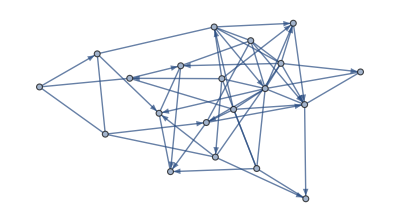

```mathematica
𝒢=RandomMixedGraph[{20,54},.77]
```

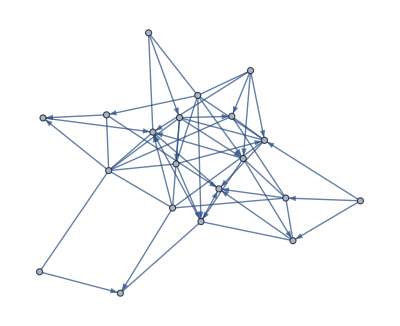

```mathematica
ℋ=RandomMixedGraph[{20,54},.77]
```

```mathematica
Table[GraphProduct[𝒢,ℋ, op, 
  PlotLabel -> Style[op, 8]], {op, {"Cartesian", "Conormal", 
   "Lexicographical", "Normal", "Rooted", "Tensor"}}]
```

{-Graphics-,,,-Graphics-,-Graphics-,-Graphics-}

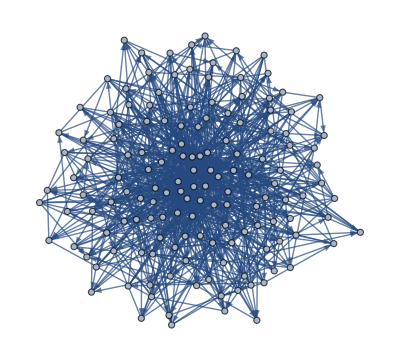

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[148,7],.5]
```

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/MixedGraphs

PeterBurbery`MixedGraphs`

PeterBurbery/MixedGraphs/Mixed_Graphs/ref/RandomMixedGraph

### Keywords

### Syntax Templates